```mathematica
ClearAll;

Off[LinearSolve::luc]
Off[$RecursionLimit::reclim2]
colo=ColorData[3,"ColorList"][[{6,2,4}]]
```

{RGBColor[0.00784313725490196, 0.5098039215686274, 0.9294117647058824],RGBColor[0.996078431372549, 0.3607843137254902, 0.027450980392156862],RGBColor[0.5411764705882353, 0.7137254901960784, 0.027450980392156862]}

1)  set J and calc. (N̂)_ij^J and (Ĥ)_ij^J                      untainted/*.exe  boundstate with INQUA_N as in RHS calc.
2)

```mathematica
HC=197.32858;
MN=(938.2796+939.5731)/2.;
MUL=1;
pi="-";

suffix="64";

litpath3He="/home/kirscher/kette_repo/ComptonLIT/mul_helion_"<>suffix<>"/";
exportpath3He="/home/kirscher/kette_repo/ComptonLIT/data/LITs/";

LIThamDET[hh_,nn_,σr_,σi_,B0_]:=Det[hh-(B0+σr+I σi) nn];
LIThamEV[hh_,nn_,σr_,σi_,B0_]:=Eigenvalues[hh-(B0+σr+I σi) nn];

LofM[jjJ_,mmJ_,sR_,sI_,kk_]:=Module[{mJ=mmJ,jJ=jjJ,sigmaRange=sR,sigmaI=sI},

file=litpath3He<>"lit_bas_lhs/norm-ham-litME-"<>ToString[jJ]<>"^"<>pi;
NormHamMat=ReadList[file,Number];
JbasisDim=NormHamMat[[1]];
norm=ArrayReshape[NormHamMat[[2;;JbasisDim^2+1]],{JbasisDim,JbasisDim}];ham=ArrayReshape[NormHamMat[[JbasisDim^2+2;;2 JbasisDim^2+1]],{JbasisDim,JbasisDim}];
file=litpath3He<>"LIT_SOURCE_"<>ToString[jJ]<>"^"<>pi<>"_mJ"<>ToString[mJ]<>"_MUL"<>ToString[MUL];
RHS=ReadList[file,Real,RecordLists->True];
Dimensions[norm];Dimensions[ham];
SlitDim=Dimensions[RHS[[1]]][[1]];
If[(JbasisDim==SlitDim)==False,
Print["Dim(Norm/H) ≠ Dim(S_LIT)"];
Print["Dim(Norm/H) = "<>ToString[JbasisDim]];
Print["Dim(S_LIT)   = "<>ToString[SlitDim]];
];
inhomo=RHS[[kk]];
litOfSigma={};
psilitOfSigma={};
For[n=1,n<=nbrs,n++,(
(*Subscript[σ, r]=n;Subscript[σ, i]=5;σ=Subscript[σ, r]+I Subscript[σ, i];*)
coeff=LinearSolve[ham-Conjugate[sigmaRange[[n]]+sigmaI I] norm,inhomo];
psilitOfSigma=Append[psilitOfSigma,coeff];
(* the prefactor (-)^(I_i-I_f+L-L'+nu') is +1 in this (I_i=I_f, L=L', nu=nu'="electric"=0) case *)
litOfSigma=Append[litOfSigma,Conjugate[coeff].norm.coeff];
)];

{litOfSigma,norm,ham,psilitOfSigma}
]
```

Setup of the RHS of the LIT equation  (Η̂-B_(3-helium)-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_(3-helium)]^Jm_J  (which is a vector!)

Setup of the LHS of the LIT equation  (Η̂-B_(3-helium)-σ_r-iσ_i) Ψ_LIT^Jm_J=[Ô Ψ_(3-helium)]^Jm_J  

Read Norm  ( (Ν^J)_(l_n l_m))  and Hamilton  ( (Η^J)_(l_n l_m))  Matrix dimensionality for  J={0: N_1
1: N_0+N_1+N_2
2: N_1+N_2+N_3

{12.}

J=0.5

ω=12.MeV

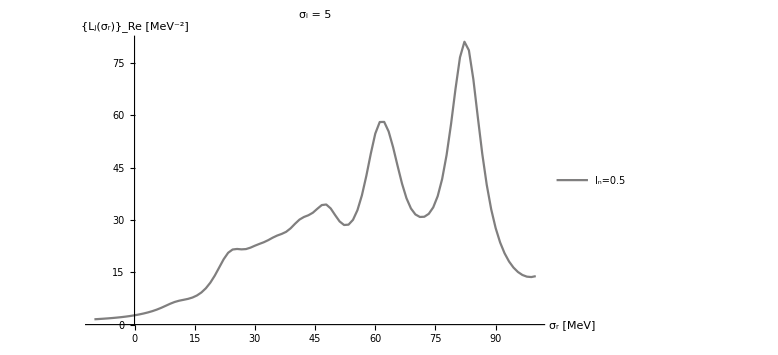

```mathematica
jlit={0.5};
j0=5;

σI=5;
smin=-10;smax=100;nbrs=100;
σR=Range[smin,smax,(smax-smin)/(nbrs-1)];
Export[litpath3He<>"sRange",{σI,N[σR]},"Table","FieldSeparators"->" ; "];

kR=ReadList[litpath3He<>"kRange.dat",Real,RecordLists->True];
anzK=kR[[1]][[1]];k0=kR[[2]][[1]];dK=kR[[3]][[1]];
anzK=1;
photK0=1;
kL=Table[k0+(photK0+n) dK,{n,anzK}]

ImLitjs={};ReLitjs={};
For[nJ=1,nJ≤Length[jlit],nJ++,(
	Print["J="<>ToString[jlit[[nJ]]]];
ImLits={};ReLits={};
Do[
Print["ω="<>ToString[kL[[nPhot]]]<>"MeV"];
Lit={};
Mats={};

For[mmj=-jlit[[nJ]],mmj≤jlit[[nJ]],mmj++,(
coflis=LofM[jlit[[nJ]],mmj,σR,σI,nPhot][[4]]//Flatten;
coflist=Transpose[{Re[coflis],Im[coflis]}];
filen=litpath3He<>"COEFFS_LIT_J"<>ToString[jlit[[nJ]]]<>"mJ"<>ToString[mmj];
Export[filen,coflist,"Table","FieldSeparators"->" ; "];
)];
            Mats=Append[Mats,{LofM[jlit[[nJ]],jlit[[nJ]],σR,σI,nPhot][[2]],LofM[jlit[[nJ]],jlit[[nJ]],σR,σI,nPhot][[3]]}];

Ltmp= Sum[Table[LofM[jlit[[nJ]],m,σR,σI,nPhot][[1]],{m,-jlit[[nJ]],jlit[[nJ]]}][[i]],{i,1,2 jlit[[nJ]]+1}];
Lit=Append[Lit,Transpose[{σR,Ltmp}]];
ImLit=Transpose[{Re[Lit][[1]][[All,1]],Im[Lit][[1]][[All,2]]}];
ImLits=Append[ImLits,ImLit];
filen=exportpath3He<>"imag_LIT_J_"<>ToString[jlit[[nJ]]]<>"_k_"<>ToString[kL[[nPhot]]]<>"_"<>suffix;
	   Export[filen,ImLit,"Table","FieldSeparators"->" ; "];
	   ReLit=Transpose[{Re[Lit][[1]][[All,1]],Re[Lit][[1]][[All,2]]}];
ReLits=Append[ReLits,ReLit];

filen=exportpath3He<>"real_LIT_J_"<>ToString[jlit[[nJ]]]<>"_k_"<>ToString[kL[[nPhot]]]<>"_"<>suffix;
Export[filen,ReLit,"Table","FieldSeparators"->" ; "];
,{nPhot,anzK}];
AppendTo[ImLitjs,ImLits];AppendTo[ReLitjs,ReLits];
)];

file=litpath3He<>"E0.dat";
EO=Read[file];Close[file];

z=List[];
For[nJ=1,nJ≤Length[jlit],nJ++,(
atmp=ListPlot[ReLitjs[[nJ]],PlotRange->Full,ImageSize->Large,Joined->True,PlotStyle->{ColorData[7,"ColorList"][[nJ]]},LabelStyle->Directive[Larger],PlotLegends->{"I_n="<>ToString[jlit[[nJ]]]}];
AppendTo[z,atmp];
)];
Show[z,AxesLabel->{"σ_r [MeV]","{L_j(σ_r)}_Re [MeV^-2]"},LabelStyle->Directive[Larger],PlotRange->Full,PlotLabel->"σ_i = "<>ToString[σI]]

parameterFilePath=exportpath3He<>"parameter_"<>suffix;
If[FileExistsQ[parameterFilePath],DeleteFile[parameterFilePath]];
file=CreateFile[parameterFilePath];
WriteString[file,"HC = ", HC,"\n"];
WriteString[file,"MN = ", MN,"\n"];
WriteString[file,"MUL = ",MUL,"\n"];
WriteString[file,"pi = ",pi,"\n"];
WriteString[file,"suffix = ",suffix,"\n"];
WriteString[file,"jlit = ",jlit,"\n"];
WriteString[file,"j0 = ",j0,"\n"];
WriteString[file,"sigmaI = ",σI,"\n"];
WriteString[file,"kRange = ",kL];
```

```mathematica
Eigenvalues[norm]//MatrixForm
Eigenvalues[{ham,norm}]//MatrixForm
```

(439463.
8014.07
734.698
55.2996
4.03187
0.364615
0.0573858
0.0206611
0.0077875
0.000810679
0.000372757
0.0000475245
0.0000102056
1.16362×10^-6
2.6753×10^-7
7.78851×10^-8
1.92301×10^-8
6.92234×10^-9
1.36329×10^-9
4.86817×10^-11)

(489.95
248.306
212.516
177.779
155.312
127.979
104.735
96.6955
90.7624
69.5495
60.1934
51.4194
44.6072
36.2831
30.1545
19.5285
17.4506
10.6678
5.49531
2.4226)

Diagnostics:
i) LIT-RGM-basis dependence

J=0.5   ω=0.202MeV

J=1.5   ω=0.202MeV

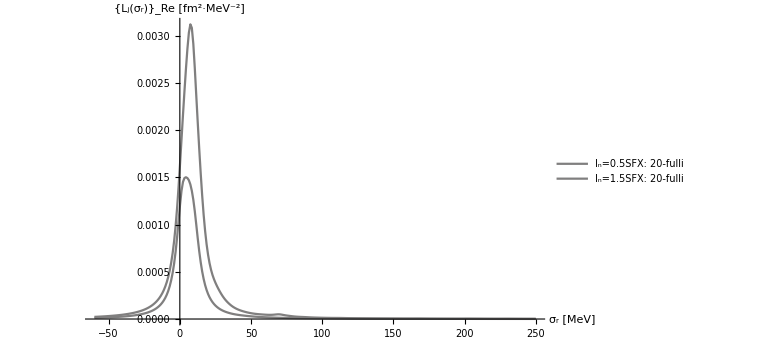

```mathematica
suffices={"20-fulli"};
jlit={0.5,1.5};
j0=0.5;

sR=ToExpression[Import[litpath3He<>"sRange","Table","FieldSeparators"->" ; "]];
σI=sR[[1]];smin=sR[[2]][[1]];smax=sR[[2]][[-1]];nbrs=Length[sR[[2]]];
σR=Range[smin,smax,(smax-smin)/(nbrs-1)];

kR=ReadList[litpath3He<>"kRange.dat",Real,RecordLists->True];
anzK=kR[[1]][[1]];k0=kR[[2]][[1]];dK=kR[[3]][[1]];
anzK=1;
photK0=1;

ImLitjsss={};ReLitjsss={};
For[nS=1,nS≤Length[suffices],nS++,(
ImLitjss={};ReLitjss={};

For[nJ=1,nJ≤Length[jlit],nJ++,(

ImLits={};ReLits={};
For[photK=photK0,photK≤photK0+anzK-1,photK++,(
kk=k0+photK dK;
Print["J="<>ToString[jlit[[nJ]]]<>"   ω="<>ToString[kk]<>"MeV"];
filen=exportpath3He<>"imag_LIT_J_"<>ToString[jlit[[nJ]]]<>"_k_"<>ToString[kk]<>"_"<>suffices[[nS]];
ImLit=ToExpression[Import[filen,"Table","FieldSeparators"->" ; "]];
ImLits=Append[ImLits,ImLit];
filen=exportpath3He<>"real_LIT_J_"<>ToString[jlit[[nJ]]]<>"_k_"<>ToString[kk]<>"_"<>suffices[[nS]];
ReLit=ToExpression[Import[filen,"Table","FieldSeparators"->" ; "]];
ReLits=Append[ReLits,ReLit];
)];
AppendTo[ImLitjss,ImLits];AppendTo[ReLitjss,ReLits];
)];
AppendTo[ImLitjsss,ImLitjss];AppendTo[ReLitjsss,ReLitjss];
)];

file=litpath3He<>"E0.dat";
EO=Read[file];Close[file];

z=List[];
For[nS=1,nS≤Length[suffices],nS++,(
For[nJ=1,nJ≤Length[jlit],nJ++,(
atmp=ListLinePlot[ReLitjsss[[nS]][[nJ]],PlotRange->Full,ImageSize->Large,Joined->True,PlotStyle->{ColorData[7,"ColorList"][[nS]]},LabelStyle->Directive[Larger],PlotLegends->{"I_n="<>ToString[jlit[[nJ]]]<>"SFX: "<>ToString[suffices[[nS]]]}];
AppendTo[z,atmp];
)];
)];Show[z,AxesLabel->{"σ_r [MeV]","{L_j(σ_r)}_Re [fm^2·MeV^-2]"},PlotRange->Full]
```